## Hubbard Model

```mathematica
(*The matrix A1 is the Hamiltonian corresponding to the Hubbard model. It is straightforward to build up by sandwiching the Hubbard Hamiltonian in between two state vectors corresponding to the position in the matrix. For example, A_11 = <phi_1|H|phi_2>.*)
```

```mathematica
A1={{0,0,0,0,0,0},{0,0,0,-t,-t,0},{0,0,0,-t, -t,0},{0,-t,-
t,U,0,0},{0,-t,-t,0,U,0},{0,0,0,0,0,0}};A1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -t | -t | 0
0 | 0 | 0 | -t | -t | 0
0 | -t | -t | U | 0 | 0
0 | -t | -t | 0 | U | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
eq1=Eigensystem[A1]//Simplify
```

{{0,0,0,U,1/2 (U-√(16 t^2+U^2)),1/2 (U+√(16 t^2+U^2))},{{0,0,0,0,0,1},{0,-1,1,0,0,0},{1,0,0,0,0,0},{0,0,0,-1,1,0},{0,(4 t)/(-U+√(16 t^2+U^2)),(4 t)/(-U+√(16 t^2+U^2)),1,1,0},{0,-(4 t)/(U+√(16 t^2+U^2)),-(4 t)/(U+√(16 t^2+U^2)),1,1,0}}}

```mathematica
(*Based on the two limiting situations discussed in the lecture note by M. Suzuki - Lecture note on solid state physics Superexchange interaction - we know that the ground state is the 5th eigenstate.*)
```

```mathematica
Eg=eq1[[1,5]]
```

1/2 (U-√(16 t^2+U^2))

```mathematica
(*By defining x and y as the ratio t/U and U/t, respectively, we can expand the expression for the eigenvalue based on the magnitudes of U and t, for example when U >> t or t >> U.*)
```

```mathematica
Eg11=Eg/.t-> x U//Simplify[#,U>0]&
```

1/2 (U-U √(1+16 x^2))

```mathematica
(*Power expansion to the 3rd order, when x->0, i.e. U >> t. This corresponds to the Mott insulator, for which the strong Coulomb repulsion U between electrons with different spin states in the same atom prevents the electrons from hopping in between atoms, thus insulator. If not considering U, the material will be predicted to be metal according to the band theory, and this is why such kind of material is given a special name - Mott insulator.*)
```

```mathematica
Eg12=Series[Eg11,{x,0,3}]//Normal
```

-4 U x^2

```mathematica
(*Next, we worry about the limitation t >> U.*)
```

```mathematica
Eg21=Eg/.U-> t y//Simplify[#,t>0]&
```

1/2 t (y-√(16+y^2))

```mathematica
(*Power expansion to the 3rd order when t->0, i.e. t >> U.*)
```

```mathematica
Eg22=Series[Eg21,{y,0,3}]//Normal
```

-2 t+(t y)/2-(t y^2)/16

```mathematica
(*The first four normalized eigenvectors. The 5th and 6th will not be shown due to the complex expression introduced by the normalization coefficient.*)
```

```mathematica
ϕ1=eq1[[2,1]]/(√(eq1[[2,1]].eq1[[2,1]]))
```

{0,0,0,0,0,1}

```mathematica
ϕ2=eq1[[2,2]]/(√(eq1[[2,2]].eq1[[2,2]]))
```

{0,-1/(√2),1/(√2),0,0,0}

```mathematica
ϕ3=eq1[[2,3]]/(√(eq1[[2,3]].eq1[[2,3]]))
```

{1,0,0,0,0,0}

```mathematica
ϕ4=eq1[[2,4]]/(√(eq1[[2,4]].eq1[[2,4]]))
```

{0,0,0,-1/(√2),1/(√2),0}

```mathematica
(*The expression for ϕ5 and ϕ6 can be simplified in the limit of U >> t and t >> U.*)
```

```mathematica
ϕ51=eq1[[2,5]]
```

{0,(4 t)/(-U+√(16 t^2+U^2)),(4 t)/(-U+√(16 t^2+U^2)),1,1,0}

```mathematica
(*When U >> t*)
```

```mathematica
ϕ52=ϕ51/.t->U x//Simplify[#,U>0]&//Series[#,{x,0,3}]&//Normal
```

{0,1/(2 x)+2 x-8 x^3,1/(2 x)+2 x-8 x^3,1,1,0}

```mathematica
(*When t >> U*)
```

```mathematica
ϕ53=ϕ51/.U->t y//Simplify[#,t>0]&//Series[#,{y,0,3}]&//Normal
```

{0,1+y/4+y^2/32,1+y/4+y^2/32,1,1,0}

```mathematica
ϕ61=eq1[[2,6]]
```

{0,-(4 t)/(U+√(16 t^2+U^2)),-(4 t)/(U+√(16 t^2+U^2)),1,1,0}

```mathematica
ϕ62=ϕ61/.t->U x//Simplify[#,U>0]&//Series[#,{x,0,3}]&//Normal
```

{0,-2 x+8 x^3,-2 x+8 x^3,1,1,0}

```mathematica
ϕ63=ϕ61/.U->t y//Simplify[#,t>0]&//Series[#,{y,0,3}]&//Normal
```

{0,-1+y/4-y^2/32,-1+y/4-y^2/32,1,1,0}

```mathematica
Energy=1/U eq1[[1]]/.t->U x//Simplify[#,U>0]&
```

{0,0,0,1,1/2 (1-√(1+16 x^2)),1/2 (1+√(1+16 x^2))}

```mathematica
(*Energy plot, from which we can see the 5th state is with the lowest energy, thus is the ground state.*)
```

```mathematica
Plot[Evaluate[Energy],{x,0,1},PlotStyle->{Table[Hue[0.2i],{i,0,5}],Thickness[0.01],Thickness[0.01],Thickness[0.01],Thickness[0.01],Thickness[0.01],Thickness[0.01]},Prolog->AbsoluteThickness[3],AxesLabel->{"t/U","E/U"},Background->GrayLevel[0.7]]
```

-Graphics-

## Molecular Orbital Hybridization

```mathematica
(*H1 is the Hamiltonian leading to the p-d mixing, i.e. we have:
H1|d>=Ed|d>+t|p>
H1|p>=t|d>+Ep|p>. The following is the matrix form of H1 in the p-d basis.*)
```

```mathematica
H1={{Ed,t},{t,Ep}};
```

```mathematica
eq1=Eigensystem[H1]
```

{{1/2 (Ed+Ep-√(Ed^2-2 Ed Ep+Ep^2+4 t^2)),1/2 (Ed+Ep+√(Ed^2-2 Ed Ep+Ep^2+4 t^2))},{{-(-Ed+Ep+√(Ed^2-2 Ed Ep+Ep^2+4 t^2))/(2 t),1},{-(-Ed+Ep-√(Ed^2-2 Ed Ep+Ep^2+4 t^2))/(2 t),1}}}

```mathematica
(*The antibonding state, and here we have ξ=Ed-Ep is the energy difference between the original d and p state without the hybridization.*)
```

```mathematica
ϕ1=eq1[[2,2]]//Simplify
```

{(Ed-Ep+√(Ed^2-2 Ed Ep+Ep^2+4 t^2))/(2 t),1}

```mathematica
ψAB=ϕ1/.Ed->Ep+ξ//FullSimplify
```

{(ξ+√(4 t^2+ξ^2))/(2 t),1}

```mathematica
(*The bonding state.*)
```

```mathematica
ϕ2=eq1[[2,1]]//Simplify
```

{-(-Ed+Ep+√(Ed^2-2 Ed Ep+Ep^2+4 t^2))/(2 t),1}

```mathematica
ψB=ϕ2/.Ed->Ep+ξ//FullSimplify
```

{(ξ-√(4 t^2+ξ^2))/(2 t),1}

```mathematica
(*The bonding and antibonding states are orthogonal to each other.*)
```

```mathematica
ψAB.ψB//Simplify
```

0

```mathematica
(*Energy of the antibonding state, higher than that of the bonding state given below, thus usually is the magnetic spin (lone spin) related:*)
```

```mathematica
EAB=eq1[[1,2]]/.Ed->Ep+ξ//Simplify
```

1/2 (2 Ep+ξ+√(4 t^2+ξ^2))

```mathematica
(*Taylay expansion to the 4th order in terms of t, when the energy difference between the original d and p states is much larger than t (which accounts for the charge transfer between p and d states, refer to(5.13) in the lecture note attached here: https://1drv.ms/b/s!AlZpbyasn9jtjahGEHq8-uPn2a1fcQ):*)
```

```mathematica
Series[EAB,{t,0,4}]//Simplify[#,ξ>0]&//Normal
```

Ep-t^4/ξ^3+t^2/ξ+ξ

```mathematica
(*Energy of the bonding state:*)
```

```mathematica
EB=eq1[[1,1]]/.Ed->Ep+ξ//Simplify
```

1/2 (2 Ep+ξ-√(4 t^2+ξ^2))

```mathematica
Series[EB,{t,0,4}]//Simplify[#,ξ>0]&//Normal
```

Ep+t^4/ξ^3-t^2/ξ

```mathematica
(*Energy difference between the bonding and antibonding states, and those between the hybridization states and the original p and d states:*)
```

```mathematica
DEN=EAB-EB/.Ed->Ep+ξ//Simplify
```

√(4 t^2+ξ^2)

```mathematica
DeltaE1Temp=EAB-Ed/.Ed->Ep+ξ//Simplify
```

1/2 (-ξ+√(4 t^2+ξ^2))

```mathematica
DeltaE1=Series[DeltaE1Temp,{t,0,2}]//Simplify[#,ξ>0]&//Normal
```

t^2/ξ

```mathematica
DeltaE2Temp=Ep-EB//Simplify
```

1/2 (-ξ+√(4 t^2+ξ^2))

```mathematica
DeltaE2=Series[DeltaE2Temp,{t,0,2}]//Simplify[#,ξ>0]&//Normal
```

t^2/ξ

```mathematica
(*The illustration for all the elements calculated above, where the red arrows indicate the spins:*)
```

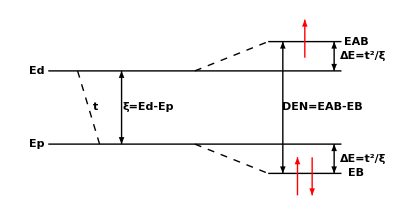

```mathematica
Show[Graphics[Line[{{0,0},{2,0}}]],Graphics[Line[{{0,0.5},{2,0.5}}]],Graphics[{Dashed,Line[{{1.0,0.5},{1.5,0.7}}]}],Graphics[Line[{{1.5,0.7},{2,0.7}}]],Graphics[{Dashed,Line[{{1.0,0},{1.5,-0.2}}]}],Graphics[Line[{{1.5,-0.2},{2,-0.2}}]],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{1.95,.0},{1.95,-.2}}]}],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{1.95,0.5},{1.95,0.7}}]}],Graphics[{Thick,Red,Arrowheads[{.05}],Arrow[{{1.8,-0.09},{1.8,-0.35}}]}],Graphics[{Thick,Red,Arrowheads[{.05}],Arrow[{{1.7,-0.35},{1.7,-0.09}}]}],Graphics[{Thick,Red,Arrowheads[{.05}],Arrow[{{1.75,0.59},{1.75,0.85}}]}],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{1.6,-0.2},{1.6,0.7}}]}],Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0.5,0},{0.5,0.5}}]}],Graphics[{Text[Style["Ed",Bold],{-0.08,0.5}]}],Graphics[{Text[Style["Ep",Bold],{-0.08,0.0}]}],Graphics[{Text[Style["ξ=Ed-Ep",Bold],{0.68,0.25}]}],Graphics[{Text[Style["DEN=EAB-EB",Bold],{1.87,0.25}]}],Graphics[{Text[Style["EAB",Bold],{2.1,0.7}]}],Graphics[{Text[Style["EB",Bold],{2.1,-0.2}]}],Graphics[{Text[Style["ΔE=t^2/ξ",Bold],{2.15,0.6}]}],Graphics[{Text[Style["ΔE=t^2/ξ",Bold],{2.15,-0.1}]}],Graphics[{Dashed,Line[{{0.35,0},{0.2,0.5}}]}],Graphics[{Text[Style["t",Bold],{0.32,0.25}]}]]
```

```mathematica
The molecular orbitals are built up from the linear combination of atomic orbitals. The atomic orbitals can be complex while the purpose of building up molecular orbitals is to make them real. The combination of p and d atomic orbitals to give the corresponding molecular orbital is shown in the following pictures:
-Graphics--Graphics-
Refer to the textbook Quantum Chemistry by Donald A. McQuarrie for details. Since the molecular orbitals are by themselves real, we don't need to square them to get real numbers. Therefore, sometimes when we come across terminologies like 'negative electron density', they actually mean the 'density' corresponding to the molecular orbital without squaring.
```

```mathematica
(*3D polar representation of |ψ> = |2p(z)> + λ|2s> with λ=-0.3, 0 and 0.3 from left to right as shown below:*)
```

```mathematica
Tlm[l_,m_,θ_] :=SphericalHarmonicY[l,m,θ,Pi]*Exp[-m I Pi]*Sqrt[2π];
```

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(-0.3Tlm[0,0,θ]+Tlm[1,0,θ])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-2,2},{-2,2},{-2,3}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.2,-0.2,1.9}]}]],Show[SphericalPlot3D[Tlm[1,0,θ]^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-2,2},{-2,2},{-2,2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.2,-0.2,1.9}]}]],Show[SphericalPlot3D[(0.3Tlm[0,0,θ]+Tlm[1,0,θ])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-2,2},{-2,2},{-2,3}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,3.0}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.2,-0.2,2.9}]}]]}]
```

-Graphics-

```mathematica
(*The hybridization between the d(3 z^2-r^2) and the p(z) orbitals. Here the blue color represents the positive density and the red color for the negative density (remember we are talking about the chemical orbitals, which are real and can be negative. For the plotting purpose, we actually square this density, but actually what we mean by positive or negative density here does mean the value without squaring.).*)
```

```mathematica
color10[θ_]:=RGBColor[-Sign[Tlm[1,0,θ]],0,Sign[Tlm[1,0,θ]]];
color11[θ_]:=RGBColor[Sign[Tlm[1,1,θ]],0,-Sign[Tlm[1,1,θ]]];
color20[θ_]:=RGBColor[-Sign[Tlm[2,0,θ]],0,Sign[Tlm[2,0,θ]]];
```

```mathematica
pzPlot=PolarPlot[{Tlm[1,0,Pi/2-θ]^2},{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.3],PlotRange->{{-1.8,1.8},{-1.8,1.8}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color10[Pi/2-θ]],ColorFunctionScaling->False,Epilog->{ Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{1.37,0},{1.38,0}}]}];
```

```mathematica
pxPlot=PolarPlot[{(Tlm[1,-1,Pi/2-θ]-Tlm[1,1,Pi/2-θ])^2/2},{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.3],PlotRange->{{-1.8,1.8},{-1.8,1.8}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color11[Pi/2-θ]],ColorFunctionScaling->False,Epilog->{ Text[Style["x",FontSize->18,Bold],{1.3,-0.08}],Arrow[{{1.37,0},{1.38,0}}]}];
```

```mathematica
d3z2Plot=PolarPlot[Tlm[2,0,Pi/2-θ]^2,{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.3],PlotRange->{{-1.8,1.8},{-1.8,1.8}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color20[Pi/2-θ]],ColorFunctionScaling->False];
```

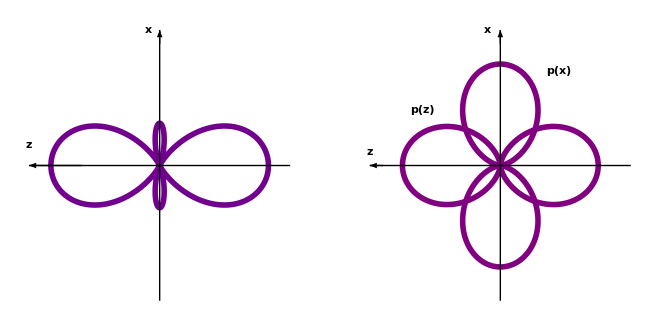

```mathematica
GraphicsRow[{Show[{Graphics[{Rotate[d3z2Plot[[1]],Pi/2,{0,0}]}],Graphics[{Arrow[{{-1.8,0},{-3,0}}]}],Graphics[{Arrow[{{0,1.8},{0,2}}]}],Graphics[{Line[{{0,-2},{0,2}}]}],Graphics[{Line[{{3.0,0},{-3.0,0}}]}],Graphics[{Text[Style["x",Large,Bold],{-0.25
,2}]}],Graphics[{Text[Style["z",Large,Bold],{-3,0.3}]}]}],Show[{Graphics[{Rotate[pzPlot[[1]],Pi/2,{0,0}]}],Graphics[{Rotate[pxPlot[[1]],Pi/2,{0,0}]}],Graphics[{Arrow[{{-1.8,0},{-2,0}}]}],Graphics[{Arrow[{{0,1.8},{0,2}}]}],Graphics[{Line[{{0,-2},{0,2}}]}],Graphics[{Line[{{2,0},{-2,0}}]}],Graphics[{Text[Style["z",Large,Bold],{-2,0.2}]}],Graphics[{Text[Style["x",Large,Bold],{-0.2,2}]}],Graphics[{Text[Style["p(x)",Large,Bold],{0.9,1.4}]}],Graphics[{Text[Style["p(z)",Large,Bold],{-1.2,0.82}]}]}]}]
```

```mathematica
(*Mixing of the d(3 z^2-r^2) and the p(z) orbitals in the following manner: |ψ> = |d(3 z^2-r^2)> + λ|p(z)>*)
```

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(0.4Tlm[1,0,θ]+Tlm[2,0,θ])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-2,2},{-2,2},{-2,5.2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,5.1}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,4.9}]}]],Show[SphericalPlot3D[(0.0Tlm[1,0,θ]+Tlm[2,0,θ])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-2,2},{-2,2},{-3,3.2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,3.1}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,2.9}]}]],Show[SphericalPlot3D[(-0.4Tlm[1,0,θ]+Tlm[2,0,θ])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-2,2},{-2,2},{-5,2.2}}],Graphics3D[{Red,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,2.1}},0.02]],Text[Style["z",FontSize->25,Bold],{-0.4,-0.4,1.9}]}]]}]
```

-Graphics-

```mathematica
(*Other orbital mixing plot will not be given here. But they should be straightforward to do, taking the demo given above as the template.*)
```

```mathematica
GraphicsRow[{Show[SphericalPlot3D[(0.3(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-0.2,0.65},{-0.65,0.65},{-0.3,0.3}}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0.6,0}},0.01]]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.6,0,0}},0.01]],Text[Style["x",FontSize->25,Bold],{0.63,0,0.}]}]],
Show[SphericalPlot3D[(0.0(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-0.3,0.5},{-0.3,0.5},{-0.3,0.3}}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0,0.6}},0.01]],Text[Style["z",FontSize->25,Bold],{-0.03,-0.03,0.35}]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.45,0,0}},0.01]],Text[Style["x",FontSize->25,Bold],{0.47,0,0.}]}]],Show[SphericalPlot3D[(-0.3(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi},Boxed->False,Axes->None,ImageSize->Scaled[1.0],ViewPoint->{0,-2,0.3},PlotRange->{{-0.5,0.35},{-0.3,0.5},{-0.3,0.3}}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0,0.6}},0.01]],Text[Style["z",FontSize->25,Bold],{-0.03,-0.03,0.35}]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.30,0,0}},0.01]],Text[Style["x",FontSize->25,Bold],{0.32,0,0.}]}]]}]
```

-Graphics-

```mathematica
color32[θ_,ϕ_]:=RGBColor[Sign[(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])],0.8,-Sign[(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])]];
```

```mathematica
vp=Options[Graphics3D,ViewPoint][[1,2]];
```

```mathematica
dx2y2DemoPlot=Show[SphericalPlot3D[(0.0(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi}, Boxed->False,Axes->None,ImageSize->Scaled[0.7],ViewPoint->{1.5396718343408038,-2.4563216626883886,1.7452491317704113},PlotRange->{{-0.55,0.55},{-0.55,0.55},{-0.55,0.55}},ColorFunction->Function[{x,y,z,θ,ϕ,r},color32[θ,ϕ]],ColorFunctionScaling->False,PlotPoints->10,MaxRecursion->4,Mesh->None],Graphics3D[{Green,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0.5,0}},0.01]]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.5,0,0}},0.01]]}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0,0.5}},0.01]]}]];
```

```mathematica
color22[θ_,ϕ_]:=RGBColor[Sign[(SphericalHarmonicY[1,1,θ,ϕ]-SphericalHarmonicY[1,-1,θ,ϕ])],0.8,-Sign[(SphericalHarmonicY[1,1,θ,ϕ]-SphericalHarmonicY[1,-1,θ,ϕ])]];
```

```mathematica
pxDemoPlot=Show[SphericalPlot3D[((SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+0.0(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi}, Boxed->False,Axes->None,ImageSize->Scaled[0.7],ViewPoint->{1.5396718343408038,-2.4563216626883886,1.7452491317704113},PlotRange->{{-0.55,0.55},{-0.55,0.55},{-0.55,0.55}},ColorFunction->Function[{x,y,z,θ,ϕ,r},color22[θ,ϕ]],ColorFunctionScaling->False,PlotPoints->10,MaxRecursion->4,Mesh->None],Graphics3D[{Green,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0.5,0}},0.01]]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.5,0,0}},0.01]]}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0,0.5}},0.01]]}]];
```

```mathematica
hybridO=Show[pxDemoPlot,dx2y2DemoPlot]
```

-Graphics3D-

```mathematica
Export["/home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/Hybrid_Demo_1.png",hybridO,ImageResolution->1200];
```

Export::nodir: Directory /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/ does not exist.

Export::noopen: Cannot open /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/Hybrid_Demo_1.png.

```mathematica
hybrid1=Show[SphericalPlot3D[(0.2(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi}, Boxed->False,Axes->None,ImageSize->Scaled[0.7],ViewPoint->{1.5396718343408038,-2.4563216626883886,1.7452491317704113},PlotRange->{{-0.7,0.7},{-0.55,0.55},{-0.55,0.55}},PlotPoints->10,MaxRecursion->4,Mesh->None],Graphics3D[{Green,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0.5,0}},0.01]]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.6,0,0}},0.01]]}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0,0.5}},0.01]]}]]
```

-Graphics3D-

```mathematica
hybrid2=Show[SphericalPlot3D[(-0.2(SphericalHarmonicY[1,-1,θ,ϕ]-SphericalHarmonicY[1,1,θ,ϕ])/Sqrt[2]+(SphericalHarmonicY[2,2,θ,ϕ]+SphericalHarmonicY[2,-2,θ,ϕ])/Sqrt[2])^2,{θ,0,Pi},{ϕ,0, 2Pi}, Boxed->False,Axes->None,ImageSize->Scaled[0.7],ViewPoint->{1.5396718343408038,-2.4563216626883886,1.7452491317704113},PlotRange->{{-0.55,0.55},{-0.55,0.55},{-0.55,0.55}},PlotPoints->10,MaxRecursion->4,Mesh->None],Graphics3D[{Green,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0.5,0}},0.01]]}],Graphics3D[{Blue,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0.5,0,0}},0.01]]}],Graphics3D[{Red,Arrowheads[0.07],Arrow[Tube[{{0,0,0},{0,0,0.5}},0.01]]}]]
```

-Graphics3D-

```mathematica
Export["/home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/Hybrid_Demo_2.png",hybrid1,ImageResolution->1200];
Export["/home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/Hybrid_Demo_3.png",hybrid2,ImageResolution->1200];
```

Export::nodir: Directory /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/ does not exist.

Export::noopen: Cannot open /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/Hybrid_Demo_2.png.

Export::nodir: Directory /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/ does not exist.

Export::noopen: Cannot open /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/Hybrid_Demo_3.png.

```mathematica
(*The region of one of the clover leaves greatly expanding along the x axis indicates the charge transfer caused by the orbitals overlapping.*)
```

```mathematica
Tlm1[l_,m_,θ_] :=SphericalHarmonicY[l,m,Pi/2.0,θ]*Exp[-m I Pi]*Sqrt[2π];
```

```mathematica
pxPlot=PolarPlot[{(Tlm1[1,-1,θ]-Tlm1[1,1,θ])^2/2},{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.3],PlotRange->{{-2.0,2.0},{-2.0,2.0}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color11[Pi/2-θ]],ColorFunctionScaling->False,Axes->False];
```

```mathematica
xAxisLine=Graphics[{Thickness[0.009],Line[{{-1.8,0},{1.8,0}}]}];
yAxisLine=Graphics[{Thickness[0.009],Line[{{0,-1.8},{0,1.8}}]}];
xAxisArrow=Graphics[{Arrowheads[0.1],Arrow[{{0,0},{2.1,0}}]}];
yAxisArrow=Graphics[{Arrowheads[0.1],Arrow[{{0,0},{0,2.1}}]}];
```

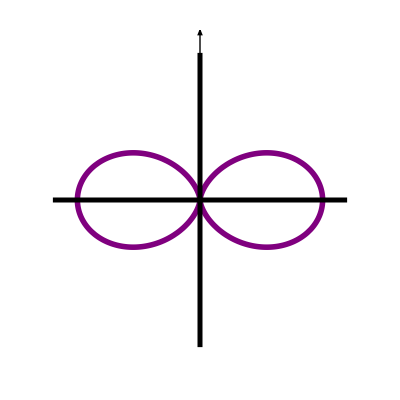

```mathematica
pxPlotO=Show[pxPlot,xAxisLine,yAxisLine,yAxisArrow]
```

```mathematica
Export["/home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/2D_Hybrid_Demo_1.png",pxPlotO,ImageResolution->1200];
```

Export::nodir: Directory /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/ does not exist.

Export::noopen: Cannot open /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/2D_Hybrid_Demo_1.png.

```mathematica
color21[θ_]:=RGBColor[Sign[(SphericalHarmonicY[2,2,Pi/2,θ]+SphericalHarmonicY[2,-2,Pi/2,θ])],0,-Sign[(SphericalHarmonicY[2,2,Pi/2,θ]+SphericalHarmonicY[2,-2,Pi/2,θ])]];
```

```mathematica
dx2y2Plot=PolarPlot[{(Tlm1[2,2,θ]+Tlm1[2,-2,θ])^2/2},{θ,0,2Pi},Ticks->None,ImageSize->Scaled[0.3],PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotStyle->{Thickness[0.01]},ColorFunction->Function[{x,y,θ,r},color21[Pi/2-θ]],ColorFunctionScaling->False,Axes->False];
```

```mathematica
xAxisLine1=Graphics[{Thickness[0.009],Line[{{-2.2,0},{2.2,0}}]}];
yAxisLine1=Graphics[{Thickness[0.009],Line[{{0,-2.2},{0,2.2}}]}];
xAxisArrow1=Graphics[{Arrowheads[0.1],Arrow[{{0,0},{2.6,0}}]}];
yAxisArrow1=Graphics[{Arrowheads[0.1],Arrow[{{0,0},{0,2.6}}]}];
```

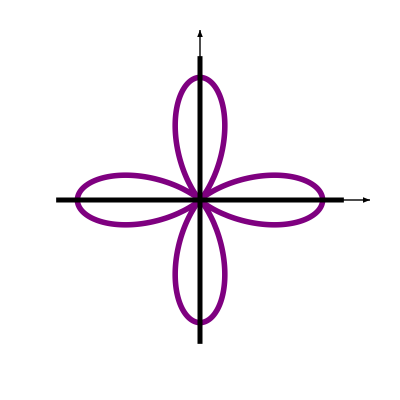

```mathematica
dx2y2PlotO1=Show[dx2y2Plot,xAxisLine1,yAxisLine1,xAxisArrow1,yAxisArrow1]
```

```mathematica
Export["/home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/2D_Hybrid_Demo_2.png",dx2y2PlotO1,ImageResolution->1200];
```

Export::nodir: Directory /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/ does not exist.

Export::noopen: Cannot open /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/2D_Hybrid_Demo_2.png.

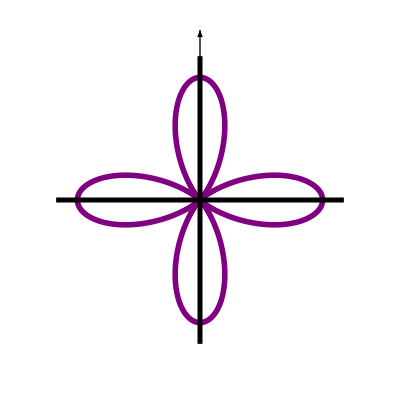

```mathematica
dx2y2PlotO2=Show[dx2y2Plot,xAxisLine1,yAxisLine1,yAxisArrow1]
```

```mathematica
Export["/home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/2D_Hybrid_Demo_3.png",dx2y2PlotO2,ImageResolution->1200];
```

Export::nodir: Directory /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/ does not exist.

Export::noopen: Cannot open /home/y8z/ZYP-Backup2/Research_Temp/CuO_NiO_NPs/CuO_DFT_BAK_May-07-2018/Charge_Density/2D_Hybrid_Demo_3.png.